```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsNEW=ReadList[FileNameJoin[{Directory[],"files/PureIntegralBasis1-111.txt"}]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
$P=2^31-1;
CayleyEntry[i_,j_]:=Module[{mat},
If[i==0 && j==0 ,
Return[0];
];
If[i==0 || j==0 ,
Return[1];
];

If[i==j,
mat=2msq[i]/.intMasses;
Return[mat];
];
If[i<j,
mat=((msq[i]/.intMasses)+(msq[j]/.intMasses)-Expand[(Sum[q[n],{n,i,j-1}])^2])/.mandelstamScalarProducts/.kinematics;
Return[mat];
];
If[i>j,
mat=CayleyEntry[j,i];
Return[mat];
];
]
cutCayley[mat_,l_]:=Module[{res},
res=mat;
res=Delete[res,l];
res=Transpose[Delete[Transpose[res],l]];
res
]
```

# Diagram 130 (Basis1-111)

hxb[0,0,1,1,0,0,1,1,0,0,0,0,0]

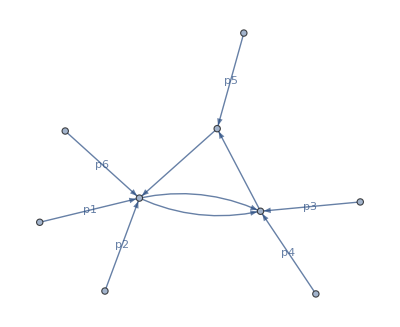

```mathematica
PureIntegralsNEW[[130]]
plotDiagram[PureIntegralsNEW[[130]]]
```

```mathematica
q[1]=p[1]+p[2]+p[6]/.p4cons;
q[2]=p[3]+p[4];
q[3]=-q[1]-q[2];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[1]=ep^3/LS*1/PR[3]
```

(0 | 1 | 1 | 1
1 | 2 mt2 | mt2-s345 | 0
1 | mt2-s345 | 0 | -s34
1 | 0 | -s34 | 0)

1/(2 root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2])

(2 ep^3 root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2])/PR[3]

# Diagram 132 (Basis1-111)

hxb[0,0,1,1,0,1,0,1,0,0,0,0,0]

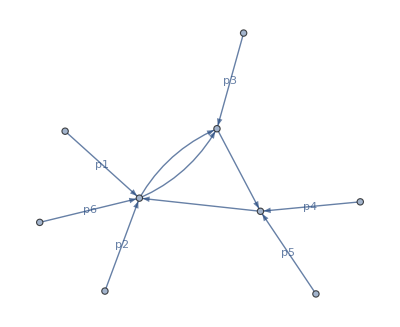

```mathematica
PureIntegralsNEW[[132]]
plotDiagram[PureIntegralsNEW[[132]]]
```

```mathematica
q[1]=p[1]+p[2]+p[6]/.p4cons;
q[2]=p[4]+p[5];
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->mt2,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[2]=ep^3/LS*1/PR[3]
```

(0 | 1 | 1 | 1
1 | 0 | mt2-s345 | 0
1 | mt2-s345 | 2 mt2 | mt2-s45
1 | 0 | mt2-s45 | 0)

1/(2 root[s345^2-2 s345 s45+s45^2])

(2 ep^3 root[s345^2-2 s345 s45+s45^2])/PR[3]

# Diagram 136 (Basis1-111)

hxb[0,1,0,1,0,0,1,1,0,0,0,0,0]

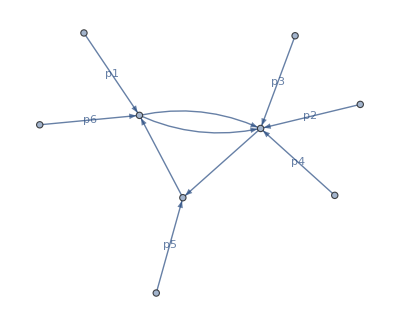

```mathematica
PureIntegralsNEW[[136]]
plotDiagram[PureIntegralsNEW[[136]]]
```

```mathematica
q[1]=p[1]+p[6]/.p4cons;
q[2]=p[5];
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->mt2,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[3]=ep^3/LS*1/PR[2]
```

(0 | 1 | 1 | 1
1 | 0 | mt2-s16 | -s234
1 | mt2-s16 | 2 mt2 | 0
1 | -s234 | 0 | 0)

1/(2 root[mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2])

(2 ep^3 root[mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2])/PR[2]

# Diagram 155 (Basis1 - 111)

hxb[1,0,0,1,0,0,1,1,0,0,0,0,0]

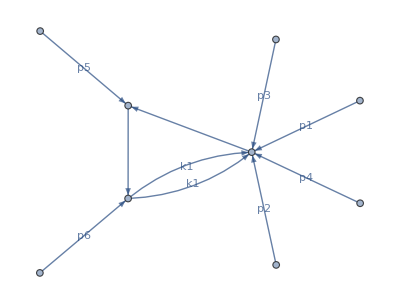

```mathematica
PureIntegralsNEW[[155]]
plotDiagram[PureIntegralsNEW[[155]]]
```

```mathematica
q[1]=p[5]/.p4cons;
q[2]=p[6]/.p4cons;
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->mt2,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[4]=ep^3/LS*1/PR[1]
```

(0 | 1 | 1 | 1
1 | 0 | 0 | -s56
1 | 0 | 2 mt2 | 0
1 | -s56 | 0 | 0)

1/(2 root[-4 mt2 s56+s56^2])

(2 ep^3 root[-4 mt2 s56+s56^2])/PR[1]

# Diagram 115/137 (Basis1 - 111)

hxb[-1,1,0,1,0,0,1,1,1,0,0,0,0]

hxb[0,1,0,1,0,0,1,1,1,0,0,0,0]

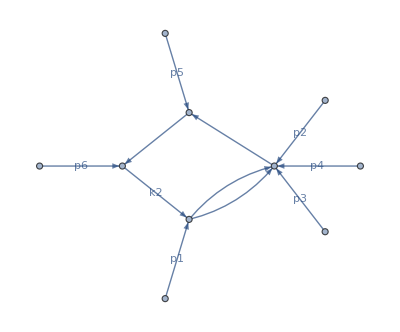

-ep^3 (-1+2 ep) root[-4 mt2 s56+s56^2]

-(ep^3 (mt2-s16) s56)/PR[2]

```mathematica
PureIntegralsNEW[[115]]
PureIntegralsNEW[[137]]
plotDiagram[PureIntegralsNEW[[115]]]
convChangerepls={d12->Expand[Expand[p[5]*p[6]/.p4cons]/.mandelstamScalarProducts/.kinematics],d15->Expand[Expand[p[1]*p[6]/.p4cons]/.mandelstamScalarProducts/.kinematics],beta->root[1-4mt2/Expand[Expand[(p[5]+p[6])^2/.p4cons]/.mandelstamScalarProducts/.kinematics]]};
BasisChange[5]=Together[ep^3(-2 beta)(2 ep-1)(d12+mt2)/.convChangerepls]/.{root[1-(4 mt2)/s56]->1/s56 root[s56^2-4mt2 s56]}
BasisChange[6]=Together[ep^3(4 d15)(d12+mt2)/PR[2]/.convChangerepls]
```

# Diagram 185/186 (Basis1 - 111)

hxb[1,1,0,1,0,0,1,1,-1,0,0,0,0]

hxb[1,1,0,1,0,0,1,1,0,0,0,0,0]

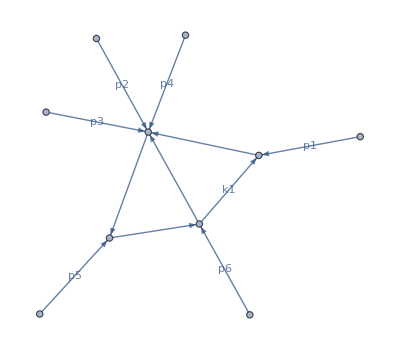

{d34→s234/2}

-ep^4 (mt2-s16+s234-s56)

-(ep^3 mt2 (s234-s56))/PR[8]

```mathematica
PureIntegralsNEW[[185]]
PureIntegralsNEW[[186]]
plotDiagram[PureIntegralsNEW[[185]]]
convChangerepls2={d34->Expand[Expand[(p[2]+p[3]+p[4])^2/2/.p4cons]/.mandelstamScalarProducts/.kinematics]}
BasisChange[7]=Together[2(d12+d15-d34+mt2)ep^4/.convChangerepls/.convChangerepls2]
BasisChange[8]=Together[2mt2 (d12-d34+mt2) ep^3/PR[8]/.convChangerepls/.convChangerepls2]
```

# Assemble basis

```mathematica
PureIntegralsTriBubble=PureIntegralsNEW[[{7,8,10,20,75,76,77,78,79,130,132,136,155,115,137,185,186}]];
PureIntegralsTriBubbleOld=PureIntegralsNEW[[{130,132,136,155,115,137,185,186}]];
PureIntegralsTriBubble[[10]]=PureIntegralsTriBubble[[10]]*BasisChange[1]
PureIntegralsTriBubble[[11]]=PureIntegralsTriBubble[[11]]*BasisChange[2]
PureIntegralsTriBubble[[12]]=PureIntegralsTriBubble[[12]]*BasisChange[3]
PureIntegralsTriBubble[[13]]=PureIntegralsTriBubble[[13]]*BasisChange[4]
PureIntegralsTriBubble[[14]]=PureIntegralsTriBubble[[15]]*BasisChange[5]
PureIntegralsTriBubble[[15]]=PureIntegralsTriBubble[[15]]*BasisChange[6]
PureIntegralsTriBubble[[16]]=PureIntegralsTriBubble[[17]]*BasisChange[7]
PureIntegralsTriBubble[[17]]=PureIntegralsTriBubble[[17]]*BasisChange[8]

Newsqrts=(Cases[PureIntegralsTriBubble,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Oldsqrts=(Cases[PureIntegralsNEW,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
sqrtSetNew=Join[Oldsqrts,Newsqrts]//DeleteDuplicates;
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],sqrtSetNew];
Export[FileNameJoin[{NotebookDirectory[],"TriBubblePureInts.txt"}],PureIntegralsTriBubble];
```

2 ep^3 hxb[0,0,2,1,0,0,1,1,0,0,0,0,0] root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2]

2 ep^3 hxb[0,0,2,1,0,1,0,1,0,0,0,0,0] root[s345^2-2 s345 s45+s45^2]

2 ep^3 hxb[0,2,0,1,0,0,1,1,0,0,0,0,0] root[mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2]

2 ep^3 hxb[2,0,0,1,0,0,1,1,0,0,0,0,0] root[-4 mt2 s56+s56^2]

-ep^3 (-1+2 ep) hxb[0,1,0,1,0,0,1,1,1,0,0,0,0] root[-4 mt2 s56+s56^2]

-ep^3 (mt2-s16) s56 hxb[0,2,0,1,0,0,1,1,1,0,0,0,0]

-ep^4 (mt2-s16+s234-s56) hxb[1,1,0,1,0,0,1,1,0,0,0,0,0]

-ep^3 mt2 (s234-s56) hxb[1,1,0,1,0,0,1,2,0,0,0,0,0]

{mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,-4 mt2 s56+s56^2}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2}

```mathematica
PureIntegralsTriBubble
```

{((2 ep-13 ep^2+27 ep^3-18 ep^4) hxb[1,0,0,1,0,0,1,0,0,0,0,0,0])/s56,((2 ep-13 ep^2+27 ep^3-18 ep^4) hxb[0,0,1,1,0,0,1,0,0,0,0,0,0])/s34,((2 ep-13 ep^2+27 ep^3-18 ep^4) hxb[0,1,0,1,0,0,1,0,0,0,0,0,0])/s234,(ep^2-5 ep^3+6 ep^4) hxb[0,1,0,1,0,0,1,0,1,0,0,0,0],(2 ep^2 hxb[1,0,0,1,0,0,0,1,0,0,0,0,0])/((1-4 ep) mt2)-(13 ep^3 hxb[1,0,0,1,0,0,0,1,0,0,0,0,0])/((1-4 ep) mt2)+(27 ep^4 hxb[1,0,0,1,0,0,0,1,0,0,0,0,0])/((1-4 ep) mt2)-(18 ep^5 hxb[1,0,0,1,0,0,0,1,0,0,0,0,0])/((1-4 ep) mt2),ep^2 s16 hxb[0,2,0,1,0,0,0,2,0,0,0,0,0],2 ep^2 mt2 hxb[0,2,0,1,0,0,0,2,0,0,0,0,0]+ep^2 mt2 hxb[0,2,0,2,0,0,0,1,0,0,0,0,0]-ep^2 s16 hxb[0,2,0,2,0,0,0,1,0,0,0,0,0],ep^2 s345 hxb[0,0,2,1,0,0,0,2,0,0,0,0,0],2 ep^2 mt2 hxb[0,0,2,1,0,0,0,2,0,0,0,0,0]+ep^2 mt2 hxb[0,0,2,2,0,0,0,1,0,0,0,0,0]-ep^2 s345 hxb[0,0,2,2,0,0,0,1,0,0,0,0,0],2 ep^3 hxb[0,0,2,1,0,0,1,1,0,0,0,0,0] root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2],2 ep^3 hxb[0,0,2,1,0,1,0,1,0,0,0,0,0] root[s345^2-2 s345 s45+s45^2],2 ep^3 hxb[0,2,0,1,0,0,1,1,0,0,0,0,0] root[mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2],2 ep^3 hxb[2,0,0,1,0,0,1,1,0,0,0,0,0] root[-4 mt2 s56+s56^2],-ep^3 (-1+2 ep) hxb[-1,1,0,1,0,0,1,1,1,0,0,0,0] root[-4 mt2 s56+s56^2],-ep^3 (mt2-s16) s56 hxb[0,2,0,1,0,0,1,1,1,0,0,0,0],hxb[1,1,0,1,0,0,1,1,-1,0,0,0,0],hxb[1,1,0,1,0,0,1,1,0,0,0,0,0]}

```mathematica
PureIntegralsTriBubble//Length
```

17

```mathematica
RemainingInts=DeleteElements[PureIntegralsNEW[[112;;]],PureIntegralsTriBubbleOld];
PureIntsUpdated=Join[PureIntegralsNEW[[;;111]],PureIntegralsTriBubble[[10;;]],RemainingInts]//EchoFunction[Length];
Export[FileNameJoin[{Directory[],"files/PureIntegralBasis1-119.txt"}],PureIntsUpdated];
```

241

250

```mathematica
Directory[]
```

/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone